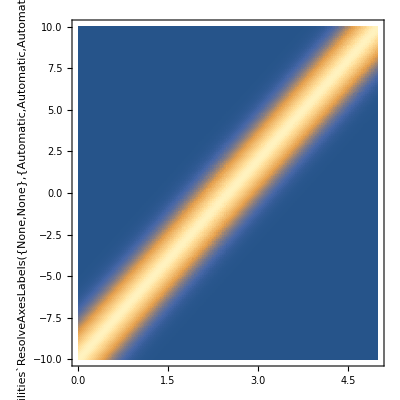

-Graphics-

-Graphics-

```mathematica
c=4;
x0=-10;
ψ[x_]:=(ⅇ^(-x^2/8+ⅈ π x))/(√(1+ⅇ^(-4 π^2)) π^(1/4))

DensityPlot[Abs[ψ[x-x0-c t]]^2,{t,0,20/c},{x,-10,10},PlotPoints->150]
DensityPlot[Abs[Re[ψ[x-x0-c t]]],{t,0,20/c},{x,-10,10},PlotPoints->150]
DensityPlot[Abs[Im[ψ[x-x0-c t]]],{t,0,20/c},{x,-10,10},PlotPoints->150]

Animate[Show[Plot[Abs[ψ[x-x0-c t]]^2,{x,-10,10},PlotRange->{0,0.6},Filling->Axis,PlotPoints->50],BoxRatios->Automatic],{t,0,20/c},AnimationRate->1, AnimationRunning->False,RefreshRate->60]
Animate[Show[Plot[{Re[ψ[x-x0-c t]],Im[ψ[x-x0-c t]]},{x,-10,10},PlotRange->{-0.8,0.8},Filling->Axis,PlotPoints->50],BoxRatios->Automatic],{t,0,20/c},AnimationRate->1, AnimationRunning->False,RefreshRate->60]
```